这里p是51个已知的梅森质数指标。

```mathematica
p={2,3,5,7,13,17,19,31,61,89,107,127,521,607,1279,2203,2281,3217,4253,4423,9689,9941,11213,19937,21701,23209,44497,86243,110503,132049,216091,756839,859433,1257787,1398269,2976221,3021377,6972593,13466917,20996011,24036583,25964951,30402457,32582657,37156667,42643801,43112609,57885161,74207281,77232917,82589933}
```

{2,3,5,7,13,17,19,31,61,89,107,127,521,607,1279,2203,2281,3217,4253,4423,9689,9941,11213,19937,21701,23209,44497,86243,110503,132049,216091,756839,859433,1257787,1398269,2976221,3021377,6972593,13466917,20996011,24036583,25964951,30402457,32582657,37156667,42643801,43112609,57885161,74207281,77232917,82589933}

2.19233×10^7

```mathematica
DistributionFitTest[p,Automatic,"HypothesisTestData"]["TestDataTable",All]
```

```mathematica
Ratios[p]//N
```

{1.5,1.66667,1.4,1.85714,1.30769,1.11765,1.63158,1.96774,1.45902,1.20225,1.18692,4.10236,1.16507,2.10708,1.72244,1.03541,1.41035,1.32204,1.03997,2.19059,1.02601,1.12795,1.77803,1.08848,1.06949,1.91723,1.93818,1.2813,1.19498,1.63645,3.50241,1.13556,1.46351,1.11169,2.1285,1.01517,2.30775,1.93141,1.55908,1.14482,1.08023,1.1709,1.07171,1.14038,1.14768,1.01099,1.34265,1.28197,1.04077,1.06936}

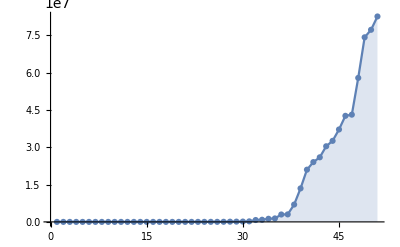

```mathematica
ListPlot[p,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
p41=Select[p,Mod[#,4]==1&]
TwoSquares[n_]=PowersRepresentations[n,2,2];
TwoSquares/@p41
```

{5,13,17,61,89,521,2281,3217,4253,9689,9941,11213,19937,21701,23209,44497,132049,859433,1398269,2976221,3021377,6972593,13466917,30402457,32582657,42643801,43112609,57885161,74207281,77232917,82589933}

{{{1,2}},{{2,3}},{{1,4}},{{5,6}},{{5,8}},{{11,20}},{{16,45}},{{9,56}},{{38,53}},{{35,92}},{{70,71}},{{67,82}},{{76,119}},{{26,145}},{{40,147}},{{64,201}},{{120,343}},{{187,908}},{{610,1013}},{{1189,1250}},{{244,1721}},{{352,2617}},{{2241,2906}},{{3291,4424}},{{3536,4481}},{{285,6524}},{{3880,5297}},{{2444,7205}},{{2716,8175}},{{2329,8474}},{{5122,7507}}}

```mathematica
p43=Select[p,Mod[#,4]==3&]
```

```mathematica
{3,7,19,31,107,127,607,1279,2203,4423,86243,110503,216091,756839,1257787,20996011,24036583,25964951,37156667}
Table[PowersRepresentations[n,3,2],{n,p43}]；
```

{3,7,19,31,107,127,607,1279,2203,4423,86243,110503,216091,756839,1257787,20996011,24036583,25964951,37156667}

```mathematica
Table[{y=Floor@Sqrt@x,ModularInverse[y,x],z=Ceiling@Sqrt@x,ModularInverse[z,x]},{x,p}]
```

ModularInverse::ninv: 2 不是不可逆模 2.

{{1,1,2,ModularInverse[2,2]},{1,1,2,2},{2,3,3,2},{2,4,3,5},{3,9,4,10},{4,13,5,7},{4,5,5,4},{5,25,6,26},{7,35,8,23},{9,10,10,9},{10,75,11,39},{11,104,12,53},{22,450,23,68},{24,430,25,170},{35,402,36,604},{46,1772,47,375},{47,728,48,1093},{56,2700,57,2314},{65,3795,66,1611},{66,4356,67,4357},{98,8206,99,5970},{99,7029,100,3877},{105,4592,106,8780},{141,10322,142,19235},{147,20520,148,5132},{152,8398,153,21237},{210,29029,211,9279},{293,8536,294,47815},{332,70895,333,14601},{363,12732,364,111371},{464,73117,465,27418},{869,391048,870,235751},{927,190058,928,302839},{1121,301824,1122,402447},{1182,718062,1183,37823},{1725,2361998,1726,1739865},{1738,655385,1739,2753814},{2640,1856717,2641,533307},{3669,1460843,3670,6960965},{4582,12055981,4583,16936996},{4902,6908924,4903,14280760},{5095,1905965,5096,2124683},{5513,1626832,5514,22622648},{5708,24676739,5709,6614696},{6095,16380634,6096,10904409},{6530,19388889,6531,35546295},{6566,3578491,6567,25629911},{7608,39312911,7609,45987094},{8614,65222118,8615,19372278},{8788,64849988,8789,55835471},{9087,26784696,9088,20020425}}